```mathematica
J=10
ℏ=1
T=0.1
β=1/T
z=1
Γ=5
Ns=1000
Nl=500
```

10

1

0.1

10.

1

5

1000

500

```mathematica
y[x]=(√(Γ^2+J^2*x^2*z^2)+J*x*z)/Γ
```

1/5 (10 x+√(25+100 x^2))

```mathematica
(y[x])^2
```

((J x z+√(J^2 x^2 z^2+Γ^2))^2)/Γ^2

```mathematica
m[x]=Simplify[ℏ*((y[x])^2-1)/((y[x])^2+1)*Tanh[β*ℏ*(√(Γ^2+J^2*x^2*z^2))/2]]
```

(2 x (2 x+√(1+4 x^2)) Tanh[25. √(1+4 x^2)])/(1+4 x^2+2 x √(1+4 x^2))

```mathematica
F[x]=-T*Ns*Log[2*Cosh[β*ℏ*(√(Γ^2+J^2*x^2*z^2))/2]]
```

-100. Log[2 Cosh[5. √(25+100 x^2)]]

```mathematica
H[x]=Simplify[F[x]+z*x*J*Ns*m[x]-J*Nl*(m[x])^2]
```

-100. Log[2 Cosh[25. √(1+4 x^2)]]+(20000 x^2 (2 x+√(1+4 x^2)) Tanh[25. √(1+4 x^2)])/(1+4 x^2+2 x √(1+4 x^2))-(20000 x^2 (2 x+√(1+4 x^2))^2 Tanh[25. √(1+4 x^2)]^2)/((1+4 x^2+2 x √(1+4 x^2))^2)

```mathematica
f[x]=D[H[x], x]
```

(2.×10^6 x^3 (2 x+√(1+4 x^2)) Sech[25. √(1+4 x^2)]^2)/(√(1+4 x^2) (1+4 x^2+2 x √(1+4 x^2)))-(10000. x Tanh[25. √(1+4 x^2)])/(√(1+4 x^2))-(20000 x^2 (2 x+√(1+4 x^2)) (8 x+(8 x^2)/(√(1+4 x^2))+2 √(1+4 x^2)) Tanh[25. √(1+4 x^2)])/((1+4 x^2+2 x √(1+4 x^2))^2)+(20000 x^2 (2+(4 x)/(√(1+4 x^2))) Tanh[25. √(1+4 x^2)])/(1+4 x^2+2 x √(1+4 x^2))+(40000 x (2 x+√(1+4 x^2)) Tanh[25. √(1+4 x^2)])/(1+4 x^2+2 x √(1+4 x^2))-(4.×10^6 x^3 (2 x+√(1+4 x^2))^2 Sech[25. √(1+4 x^2)]^2 Tanh[25. √(1+4 x^2)])/(√(1+4 x^2) (1+4 x^2+2 x √(1+4 x^2))^2)+(40000 x^2 (2 x+√(1+4 x^2))^2 (8 x+(8 x^2)/(√(1+4 x^2))+2 √(1+4 x^2)) Tanh[25. √(1+4 x^2)]^2)/((1+4 x^2+2 x √(1+4 x^2))^3)-(40000 x^2 (2+(4 x)/(√(1+4 x^2))) (2 x+√(1+4 x^2)) Tanh[25. √(1+4 x^2)]^2)/((1+4 x^2+2 x √(1+4 x^2))^2)-(40000 x (2 x+√(1+4 x^2))^2 Tanh[25. √(1+4 x^2)]^2)/((1+4 x^2+2 x √(1+4 x^2))^2)

```mathematica
Plot of (∂H)/(∂x) vx x... i.e if we get a solution or not:
```

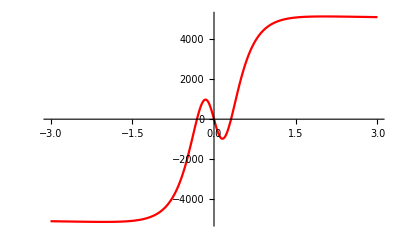

```mathematica
Plot[f[x],{x,-3,3},PlotStyle->Red,PlotRange->Full]
```

```mathematica
parametric Plot of m(x) vs H(x)::
```

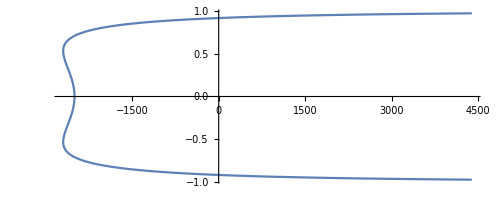

```mathematica
ParametricPlot[Evaluate[{H[x],m[x]}],{x,-2,2}]
```

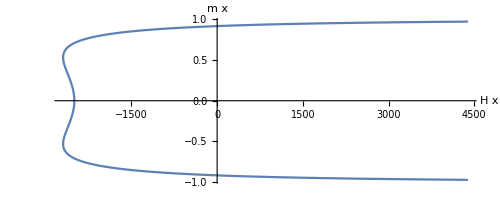

```mathematica
Show[%65,AxesLabel->{HoldForm[H x],HoldForm[m x]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
parametric Plot of  dH/dx vs m(x) ....   m in y axis, H'[x] in x axis::
```

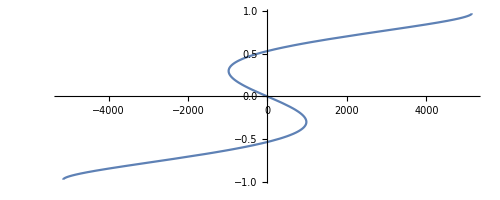

```mathematica
ParametricPlot[Evaluate[{f[x],m[x]}],{x,-2,2}]
```